```mathematica
decode[nn_, deg_, count_]:=
Module[{output, n=nn},
output = Range[count];
n=n-1;
For[i=1,i≤ count,i++,
{n,output[[count+1-i]]}= QuotientRemainder[n,deg+1];
];
output
]
```

```mathematica
constructPP[list_, cons_] :=
Module[{power},
power = 1;
For[i=1,i≤ Length[list],i++,
power = power*cons[[i]]^list[[i]];
];
power
]
```

```mathematica
handelmanConstraints[poly_,vars_, cons_, deg_] :=
Module[{consCount, degreeList, decodeNew, powerProduct,constructPPNew,lpvarList,lpvar,target, coefList,i, newCons},
consCount = Length[cons];
decodeNew [x_] := decode[x,deg, consCount];
degreeList = Map[decodeNew, Range[(deg+1)^consCount]];
constructPPNew[x_] := constructPP[x, cons];
powerProduct= Map[constructPPNew, degreeList];
lpvarList = Array[lpvar, (deg+1)^consCount];
target = poly- Total[lpvarList*powerProduct]; (*target is a zero polynomial*)
coefList = Flatten[CoefficientList[target,vars]];
newCons = {};
For[i=1,i≤ Length[coefList],i++,
AppendTo[newCons, coefList[[i]]== 0];
];
For[i=1,i≤ Length[lpvarList],i++,
AppendTo[newCons, lpvarList[[i]]≥  0];
];
{newCons,lpvarList}
]
```

```mathematica
vars = {x, y};
(*≤0*)
domainCons = {4-x, x+4, 4-y, y+4};(*≥ *)
unsafeCons = {y-2};
initCons = {x, 0.5-x, 1-y, y};
deg = 5;

monoList = MonomialList[(1+x+y)^deg];
bcCoefList = Array[bcCoef, Length[monoList]];
bc = Total[bcCoefList*monoList];
bcf = ReplaceAll[bc,{x-> 8/9*x-1/18*y+0.01*dd, y-> y+x}];
ebc = Integrate[bcf,{dd,-1,1}]*1/2;

{c1,v1} = handelmanConstraints[-bc+gamma,vars, initCons, deg];
{c2,v2} = handelmanConstraints[bc, vars,domainCons,deg];
{c3,v3} = handelmanConstraints[bc-ebc,vars, domainCons,deg];
{c4,v4} = handelmanConstraints[bc-ebc-1,vars, Union[domainCons,unsafeCons],deg];
```

```mathematica
Print["Number of Monomials, ", Binomial[deg+Length[vars],deg]];
Print["Number of power product, (lp variables)", (deg+1)^Length[domainCons]];
```

Number of Monomials, 28

Number of power product, (lp variables)2401

```mathematica
sol = LinearOptimization[gamma,Union[c1,c2,c3,c4],Union[v1,v2,v3,v4,bcCoefList,{gamma}]];
Print["bc:",ReplaceAll[bc,sol]];
Print["ebc:", ReplaceAll[ebc,sol]];
Print[ReplaceAll[gamma,sol]]
```

bc:0.

ebc:0.

0.

```mathematica
sol
```

```mathematica
bcNum = ReplaceAll[bc,sol];
FindInstance[bcNum< 0&&4-x≥ 0&& x+4≥ 0 &&4-y≥ 0&& y+4≥ 0,{x,y}]
```

{{x→-4.,y→0.}}

```mathematica
bcNum/.{x->-4,y->0}
```

-0.0505891

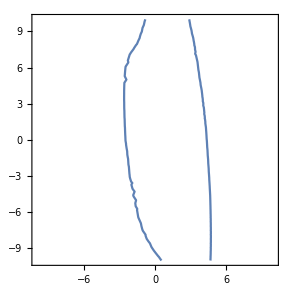

```mathematica
ContourPlot[bcNum== 0,{x,-10,10},{y,-10,10}]
```

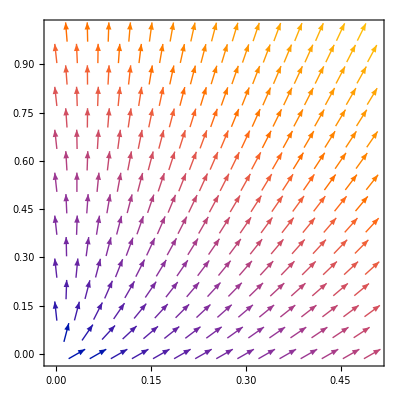

```mathematica
VectorPlot[{8/9*x-1/18*y, y+x},{x,0,0.5},{y,0,1}]
```